```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->NotebookDirectory[]]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,2->3],{S[1],S[1]}->{S[1],S[1],S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{NotebookDirectory[],"ScalarProxy"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"ScalarProxy"}]];
```

```mathematica
(*Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];*)
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{-p1,-p2},OutgoingMomenta->{k1,k2,k3},LoopMomenta->{},ChangeDimension->4,List->False]// ExpandScalarProduct//FeynAmpDenominatorExplicit (*SetMandelstam[x1,{ p1 , p2, k1 , k2 ,k3} ,{0 , 0 , 0 , 0,0} ];
```

```mathematica
amp[0]//Contract//ExpandScalarProduct//Simplify;
```

```mathematica
(*amp[1] = amp[0] * x[1,2]// Simplify;
```

```mathematica
(*amp[2] = amp[1]/.x[1,2]->0;
```

```mathematica
(*amp[2] //Simplify
```

```mathematica
amp[1]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{-p1,-p2},OutgoingMomenta->{l1,l2,l3},LoopMomenta->{},ChangeDimension->4,List->False]// ExpandScalarProduct//FeynAmpDenominatorExplicit;
```

```mathematica
amp[1] = FeynAmpDenominatorExplicit[amp[1]];
```

```mathematica
SetMandelstam[x2,{ p1 , p2, l1 , l2 ,l3} ,{0 , 0 , m , m,0} ];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
amp[1]//Contract//ExpandScalarProduct;
```

```mathematica
amp[2]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{-p1,-p2},OutgoingMomenta->{q1,q2,q3},LoopMomenta->{},ChangeDimension->4,List->False]// ExpandScalarProduct//FeynAmpDenominatorExplicit;SetMandelstam[x3,{ p1 , p2, q1 , q2 ,q3} ,{0 , 0 , 0 , m,m} ];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
amp[2]//Contract//ExpandScalarProduct
```

```mathematica
amp[3]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{-p1,-p2},OutgoingMomenta->{r1,r2,r3},LoopMomenta->{},ChangeDimension->4,List->False]// ExpandScalarProduct//FeynAmpDenominatorExplicit;SetMandelstam[x4,{ p1 , p2, r1 , r2 ,r3} ,{0 , 0 , m , 0,m} ];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
amp[3]//Contract// SUNSimplify//ExpandScalarProduct//Simplify;
```

StringForm::sfr: Item 2 requested in "Operation `1` timed out after `2` seconds." out of range; 1 items available.

Simplify::time: Operation 300. timed out after `2` seconds.

$Aborted

```mathematica
amp[4]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{-p1,-p2},OutgoingMomenta->{s1,s2,s3},LoopMomenta->{},ChangeDimension->4,List->False]// ExpandScalarProduct//FeynAmpDenominatorExplicit;SetMandelstam[x5,{ p1 , p2, s1 , s2 ,s3} ,{0 , 0 , m , m,m} ];
```

```mathematica
amp[4]//Contract// SUNSimplify//ExpandScalarProduct//Simplify;
```

```mathematica
-g^3/m^4 * (amp[0]-amp[1]-amp[2]-amp[3]+2amp[4])
```

```mathematica
CreateFeynAmp[diags, PreFactor->1,Unitarity]
```

```mathematica
diags=InsertFields[CreateTopologies[1,1->1,ExcludeTopologies->Tadpoles],{S[1]}->{S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{NotebookDirectory[],"ScalarProxy"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"ScalarProxy"}]];
```

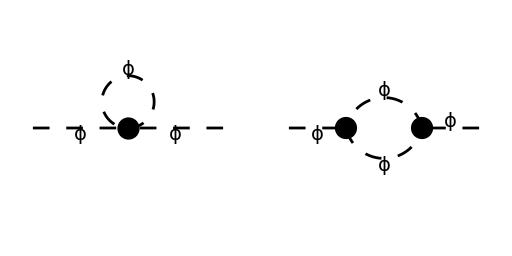

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[4]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{p1},OutgoingMomenta->{p1},LoopMomenta->{l},ChangeDimension->4,List->False]//FeynAmpDenominatorExplicit
```

-(3 g^2)/(2 Pair[Momentum[l],Momentum[l]] (-m^2+Pair[Momentum[l],Momentum[l]]))-((ⅈ g m^2-ⅈ g Pair[Momentum[l],Momentum[l]]-ⅈ g Pair[Momentum[l-p1],Momentum[l-p1]]-ⅈ g Pair[Momentum[p1],Momentum[p1]]) (ⅈ g m^2-ⅈ g Pair[Momentum[l],Momentum[l]]-ⅈ g Pair[Momentum[p1],Momentum[p1]]-ⅈ g Pair[Momentum[-l+p1],Momentum[-l+p1]]))/(2 Pair[Momentum[l],Momentum[l]] (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))

```mathematica
amp[5] = ToPaVe[amp[4],l]
```

-(3 g^2)/(2 Pair[Momentum[l],Momentum[l]] (-m^2+Pair[Momentum[l],Momentum[l]]))+(g^2 Pair[Momentum[l],Momentum[l]])/(2 (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))+(g^2 Pair[Momentum[l-p1],Momentum[l-p1]])/(2 (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))-(g^2 (m^2-Pair[Momentum[p1],Momentum[p1]]))/((-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))-(g^2 Pair[Momentum[l-p1],Momentum[l-p1]] (m^2-Pair[Momentum[p1],Momentum[p1]]))/(2 Pair[Momentum[l],Momentum[l]] (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))+(g^2 (m^2-Pair[Momentum[p1],Momentum[p1]])^2)/(2 Pair[Momentum[l],Momentum[l]] (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))+(g^2 Pair[Momentum[-l+p1],Momentum[-l+p1]])/(2 (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))+(g^2 Pair[Momentum[l-p1],Momentum[l-p1]] Pair[Momentum[-l+p1],Momentum[-l+p1]])/(2 Pair[Momentum[l],Momentum[l]] (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))-(g^2 (m^2-Pair[Momentum[p1],Momentum[p1]]) Pair[Momentum[-l+p1],Momentum[-l+p1]])/(2 Pair[Momentum[l],Momentum[l]] (-m^2+Pair[Momentum[l],Momentum[l]]) (Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]) (-m^2+Pair[Momentum[l],Momentum[l]]-2 Pair[Momentum[l],Momentum[p1]]+Pair[Momentum[p1],Momentum[p1]]))